## Lesson 23: Step functions

## Overview

The previous lesson outlined the general procedure for solving initial value problems using the LaplaceTransform.

There are much more interesting applications of the Laplace transform in differential equations when you consider discontinuous forcing functions.

These types of equations arise frequently in the analysis of the flow of current in electric circuits.

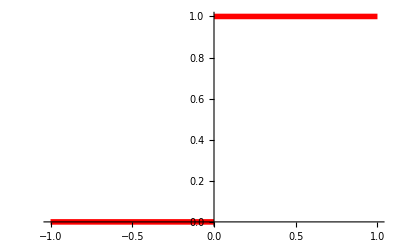

```mathematica
Plot[UnitStep[x],{x,-1,1},]
```

## Unit Step Function

There is a useful tool in mathematics to describe functions with jump discontinuities, known as the UnitStep function:

```mathematica
Plot[UnitStep[x],{x,-1,1},]
```

-Graphics-

For x≥0, this function takes the value 1 and for x<0, the function takes the value 0.

You can use this function to construct a variety of different functions:

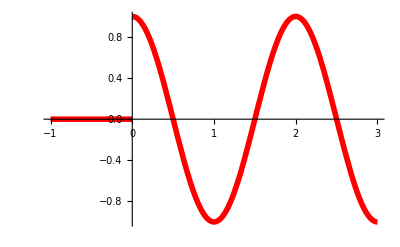

```mathematica
Plot[Cos[Pi x]UnitStep[x],{x,-1,3},]
```

## Example 1: Construct a Box Function

Construct the function corresponding to the following plot:

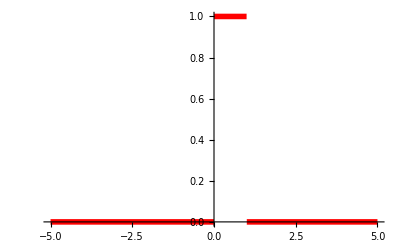

```mathematica
Plot[HeavisideTheta[x]-HeavisideTheta[x-1],{x,-5,5},]
```

The unit step function U(x) appears as follows:

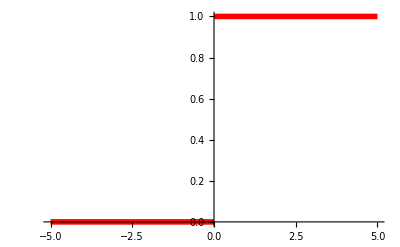

```mathematica
Plot[UnitStep[x],{x,-5,5},]
```

## Example 1: Construct a Box Function

The function can be shifted by using a substitution of variables:

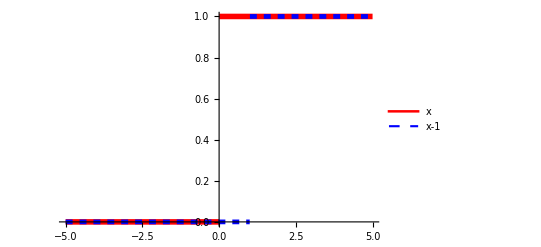

```mathematica
Plot[{UnitStep[x],UnitStep[x-1]},{x,-5,5},]
```

By taking the difference of these two unit step functions, you can construct the desired plot:

```mathematica
Plot[UnitStep[x]-UnitStep[x-1],{x,-5,5},]
```

-Graphics-

## Example 1: Construct a Box Function

This can be done more simply by defining a Piecewise function:

```mathematica
Plot[Piecewise[{{1,0<x<1}}],{x,-5,5},]
```

-Graphics-

In fact, this function is so common that it is built into the Wolfram Language as UnitBox:

```mathematica
Plot[UnitBox[x-1/2],{x,-5,5},]
```

-Graphics-

## Example 2: Construct a Unit Triangle

Express the function corresponding to UnitTriangle using only unit step functions:

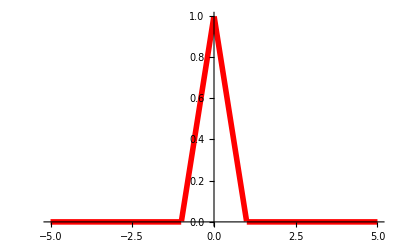

```mathematica
Plot[UnitTriangle[x],{x,-5,5},]
```

The UnitStep function U(x) appears as follows:

```mathematica
Plot[UnitStep[x],{x,-5,5},]
```

-Graphics-

## Example 2: Construct a Unit Triangle

The function can be shifted by using a substitution of variables:

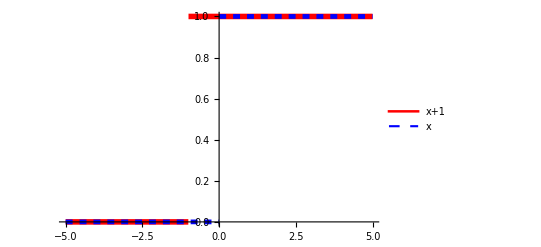

```mathematica
Plot[{UnitStep[x+1],UnitStep[x]},{x,-5,5},]
```

By taking the difference of many unit step functions, you can construct the desired plot:

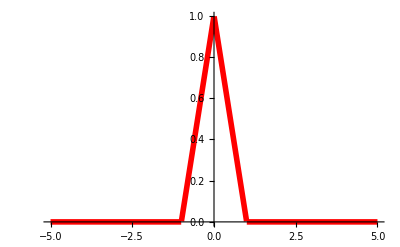

```mathematica
Plot[(x+1)UnitStep[x+1]-(2x)UnitStep[x]+(x-1)UnitStep[x-1],{x,-5,5},]
```

## Example 2: Construct a Unit Triangle

You can construct this function using Piecewise:

```mathematica
Plot[Piecewise[{{0,x<-1},{x+1,-1<x<0},{-x+1,0<x<1},{0,x>1}}],{x,-5,5},]
```

-Graphics-

This function is also built into the Wolfram Language as UnitTriangle:

```mathematica
Plot[UnitTriangle[x],{x,-5,5},]
```

-Graphics-

## Laplace Transform

The Laplace transform of a unit step function can in fact be quite easily determined:

```mathematica
Integrate[Exp[-s t] UnitStep[t-c],{t,0,∞},Assumptions->c>0]
```

ConditionalExpression[ⅇ^(-c s)/s, Re[s]>0]

This leads to an important result for the translation of a function.

For a given function f(t) defined for t≥0, the Laplace transform of the translation of the function U(t-c)f(t-c) can be written as:

L{U(t-c)f(t-c)}=e^(-c s)L{f(t)}

```mathematica
f[t_]:=Piecewise[{{Exp[-t],t≥0},{0,t<0}}]
```

Compare the Laplace transform of f(t) with U(t-c)f(t-c):

```mathematica
LaplaceTransform[f[t],t,s]
```

1/(1+s)

```mathematica
LaplaceTransform[UnitStep[t-c]f[t-c],t,s,Assumptions->c>0]
```

ⅇ^(-c s)/(1+s)

## Example 3: Piecewise Laplace Transform

If a function is defined by:

f(t)=Piecewise[{{1
1/2, 0 ≤t≤ 5
t≥5}, {0, Otherwise}}]

find L{f(t)}.

You can rewrite f(t)=1+g(t) where g(t) is defined as:

g(t)=Piecewise[{{0, t<π}, {-1/2UnitStep[t-5], t≥π}}]

Therefore, because the LaplaceTransform is linear: L{f(t)}=L{1}+L{g(t)}.

Using the previous theorem and the fact that g(t)=-1/2U(t-5) , you can have that: L{f(t)}=L{1}+e^(-5 s)L{-1/2}.

Thus, the final answer must be the following:

```mathematica
LaplaceTransform[1, t,s]+E^(-5*s)*LaplaceTransform[-1/2, t,s]
```

1/s-ⅇ^(-5 s)/(2 s)

## Example 3: Piecewise Laplace Transform

This can be confirmed by defining f(t) as a Piecewise function:

```mathematica
f[t_]:=Piecewise[{{1,0≤t<5},{1/2,t≥5},{0,t<0}}]
```

Then, by applying the Wolfram Language function LaplaceTransform to f(t), you can compute the Laplace transform of this piecewise function:

```mathematica
LaplaceTransform[f[t],t,s]
```

(ⅇ^(-5 s) (-1+2 ⅇ^(5 s)))/(2 s)

It can be seen that this is exactly equal to the previous result:

```mathematica
LaplaceTransform[1, t,s]+Exp[-5s]*LaplaceTransform[-1/2, t,s]==LaplaceTransform[f[t],t,s]//Simplify
```

True

## Example 4: Piecewise Laplace Transform

If a function is defined by

f(t)=Piecewise[{{sin(t), 0≤t≤π}, {cos(t-π)+sin(t)
0, t≥π
Otherwise}}]

find L{f(t)}.

You can rewrite f(t)=sin(t)+g(t) where g(t) is defined as:

g(t)=Piecewise[{{0, t<π}, {cos(t-π)UnitStep[t-π], t≥π}}]

Also, because the LaplaceTransform is linear:

L{f(t)}=L{sin(t)}+L{g(t)}

Using the previous theorem and the fact that:

g(t)=U(t-π)cos(t-π)

you can have that:

L{f(t)}=L{sin(t)}+e^(-π s)L{cos(t)}

Thus, the final answer must be the following:

```mathematica
LaplaceTransform[Sin[t], t,s]+Exp[-Pi s]LaplaceTransform[Cos[t], t,s]
```

1/(1+s^2)+(ⅇ^(-π s) s)/(1+s^2)

## Example 4: Piecewise Laplace Transform

This can be confirmed by defining f(t) as a Piecewise function:

```mathematica
f[t_]:=Piecewise[{{Sin[t],0≤t<Pi},{Sin[t]+Cos[t-Pi],t≥Pi},{0,t<0}}]
```

Applying LaplaceTransform to f(t), you can compute the LaplaceTransform of this piecewise function:

```mathematica
LaplaceTransform[f[t],t,s]
```

(ⅇ^(-π s) (ⅇ^(π s)+s))/(1+s^2)

It can be seen that this is exactly equal to the previous result:

```mathematica
LaplaceTransform[Sin[t],t,s]+Exp[-Pi s] LaplaceTransform[Cos[t],t,s]==LaplaceTransform[f[t],t,s]//Simplify
```

True

## Summary

This lesson further explored properties of the LaplaceTransform of step functions.

You started by constructing different piecewise functions, then proved that when a given function g(t) defined for t≥0 can be written as:

U(t-c)f(t-c)

the Laplace transform of the translation of the function L{g(t)} is:

L{g(t)}=L{U(t-c)f(t-c)}=e^(-c s)L{f(t)}

This allows you to transform a variety of discontinuous functions.

This will prove to be exceptionally useful in the solution to nonhomogeneous differential equations.